### 50 12

```mathematica
WW150={{0.25,-0.000013194480950147668},{0.5,0.00031019501993460527},{0.75,0.002717604576925877},{1.,0.02367018706977363},{1.25,0.19578871067225387},{1.5,0.5559503122153263},{1.75,0.9460873538144916},{2.,1.145759239104823},{2.25,1.2325292874917195},{2.5,1.2768727953183623},{2.75,1.2825075270726898},{3.,1.2573453205089582}};
WW250={{0.25,0.},{0.5,0.},{0.75,0.},{1.,0.},{1.25,0.00936722114783678},{1.5,0.0597452442521996},{1.75,0.16377818228531726},{2.,0.31265018931986666},{2.25,0.4852875215703426},{2.5,0.6639322562477769},{2.75,0.8224030426851879},{3.,0.9645419991274135}};
WWW150=Interpolation[WW150];
WWW250=Interpolation[WW250];
```

### 100 12

```mathematica
WW1100={{0.1,0.},{0.2,-1.0666702201226216*^-6},{0.30000000000000004,9.187078747920982*^-6},{0.4,0.00001788550426228421},{0.5,0.000053290732647651856},{0.6,0.00011765567627103429},{0.7,0.0003983514876849674},{0.7999999999999999,0.0010030874909111227},{0.8999999999999999,0.0029704772553979845},{0.9999999999999999,0.009066978072774831},{1.0999999999999999,0.023286033957274955},{1.2,0.05720781209172291},{1.3,0.11376604468976927},{1.4000000000000001,0.19215095487426498},{1.5000000000000002,0.2941487841924368},{1.6000000000000003,0.4051375737714961},{1.7000000000000004,0.5349950786172094},{1.8000000000000005,0.6594259374248531},{1.9000000000000006,0.7893438603986865},{2.0000000000000004,0.9353319212432901},{2.1000000000000005,1.051498953169258},{2.2000000000000006,1.1783386969183662},{2.3000000000000007,1.296049475497656},{2.400000000000001,1.4093842897727138},{2.500000000000001,1.524423167391128},{2.600000000000001,1.6132128212907404},{2.700000000000001,1.685649275467861},{2.800000000000001,1.7598478824173187},{2.9000000000000012,1.817857173239995},{3.0000000000000013,1.8623527848674466}};
WW2100={{0.1,0.},{0.2,0.},{0.30000000000000004,0.},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.7999999999999999,0.},{0.8999999999999999,0.},{0.9999999999999999,0.},{1.0999999999999999,0.0003957200310688715},{1.2,0.002667088485239414},{1.3,0.008493948169624534},{1.4000000000000001,0.018971346158806482},{1.5000000000000002,0.03484231373269034},{1.6000000000000003,0.0564975700551896},{1.7000000000000004,0.08536720474367843},{1.8000000000000005,0.1216689283231594},{1.9000000000000006,0.16053457107247956},{2.0000000000000004,0.21027124750976692},{2.1000000000000005,0.2626212646160044},{2.2000000000000006,0.32665272929778655},{2.3000000000000007,0.38944109855474424},{2.400000000000001,0.45584629226699647},{2.500000000000001,0.5293195746501141},{2.600000000000001,0.6022547020391618},{2.700000000000001,0.6777200712701009},{2.800000000000001,0.7589529116695976},{2.9000000000000012,0.836966945899543},{3.0000000000000013,0.9139825738301728}};
WWW1100=Interpolation[WW1100];
WWW2100=Interpolation[WW2100];
```

#### 150 12

```mathematica
W1150={{0.25,0.},{0.5,0.},{0.75,7.859514818294742*^-7},{1.,0.002230781132048738},{1.25,0.04264387559915284},{1.5,0.191101205716433},{1.75,0.44988746378470196},{2.,0.7639293213550276},{2.25,1.118274476583965},{2.5,1.4580284143979556},{2.75,1.7563217356975218},{3.,2.0314560061505706}};
W2150={{0.25,0.},{0.5,0.},{0.75,0.},{1.,0.},{1.25,0.0036277813124243677},{1.5,0.024700711406391154},{1.75,0.07382558339304351},{2.,0.1560578730379031},{2.25,0.2714662977430243},{2.5,0.4181916335203129},{2.75,0.5853311391614953},{3.,0.7757788256134119}};
WWWW1150=Interpolation[W1150];
WWWWW2150=Interpolation[W2150];
```

#### 200 12

```mathematica
WW1200={{0.25,0.},{0.5,0.},{0.75,0.000014567943697710208},{1.,0.0034447222059790063},{1.25,0.04330941783040642},{1.5,0.18282574523916534},{1.75,0.4225754605361488},{2.,0.7234881458096027},{2.25,1.0520740071366217},{2.5,1.3644189791157117},{2.75,1.6083088670940577},{3.,1.8115899374627709}};
WW2200={{0.25,0},{0.5,0},{0.75,0},{1,0},{1.25,0.0028873515320663214},{1.5,0.02006608146912996},{1.75,0.061456164744105854},{2,0.13354647259278238},{2.25,0.2395499246911103},{2.5,0.38118413161859693},{2.75,0.5520378291397025},{3,0.7573768484437469}};
WWW1200=Interpolation[WW1200];
WWW2200=Interpolation[WW2200];
```

#### 50-100-200 12

```mathematica
Plot[{WWW1100[x]+WWW1200[x],WWW1200[x]+WWW2200[x]},{x,0,3},PlotStyle->{{Thick,Black},{Black,Thick}},PlotRange->{{0,3},{0,4}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->16]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

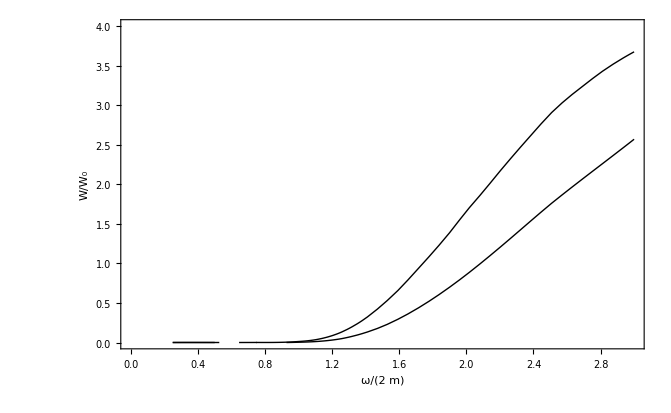

-Graphics-

```mathematica
Show[%,LabelStyle->Directive[FontFamily->"Times",FontSize->24, Black,Thin]]
```

-Graphics-

### 50 22

```mathematica
WW1150={{1.,0},{1.1,0.51},{1.2000000000000002,1.0266357922263716},{1.3000000000000003,1.6482998113796232},{1.4000000000000004,2.4009615896780053},{1.5000000000000004,2.940509341483505},{1.6000000000000005,3.4152576060038467},{1.7000000000000006,4.075195490132475},{1.8000000000000007,4.444865964928983},{1.9000000000000008,4.409005261342843},{2.000000000000001,4.036842588251251},{2.100000000000001,3.2136177819375553},{2.200000000000001,2.6818767092082805},{2.300000000000001,2.178391188434085},{2.4000000000000012,1.8029162418506428},{2.5,1.499451390812346},{2.6,1.2885371403504409},{2.7,1.0877168972087858},{2.8000000000000003,0.9626271767496124},{2.9000000000000004,0.8881653979175421},{3.,0.8575513475745847}};
WW1250={{1.,0.},{1.1,-0.0001535008684756593},{1.2000000000000002,-0.0023142499948259148},{1.3000000000000003,0.007737672102380029},{1.4000000000000004,0.023533130996765315},{1.5000000000000004,0.046267690116661105},{1.6000000000000005,0.07867685498186346},{1.7000000000000006,0.10163824726325799},{1.8000000000000007,0.1411307883642298},{1.9000000000000008,0.18193774389937464},{1.91,0.1859208397413663},{1.92,0.19015881693470116},{1.93,0.1943943885785327},{1.94,0.198151902430094745},{1.95,0.20309042549439016},{1.96,0.209656956909001},{1.97,0.21152745879764026},{1.98,0.217319564397641},{1.99,0.22977918813151274},{2.000000000000001,0.25189493458481854},{2.01,0.2203752961256955},{2.0199999999999996,0.21187301441899128},{2.0299999999999994,0.20683628428200104},{2.039999999999999,0.20335321243358342},{2.049999999999999,0.2007671971930456},{2.0599999999999987,0.19876683989923224},{2.0699999999999985,0.197177107963559},{2.0799999999999983,0.1958923720915257},{2.089999999999998,0.19484021093574574},{2.100000000000001,0.19397308322231552},{2.200000000000001,0.19039364510890372},{2.300000000000001,0.19013434283941982},{2.4000000000000012,0.1903424345967275},{2.5000000000000013,0.19012410578119432},{2.6000000000000014,0.1891658348002664},{2.7000000000000015,0.18734674440578936},{2.8000000000000016,0.18465441576606748},{2.9000000000000017,0.18112717068933262},{3.0000000000000018,0.1768349632286124}};
WWW1150=Interpolation[WW1150];
WWW1250=Interpolation[WW1250];
```

#### 100 22

```mathematica
WW11100={{0,0},{0.125,0},{0.25,0},{0375,0},{0.5,0},{0.625,0},{075,0},{0.875,0},{1.,0.01},{1.125,0.13280491563881811},{1.25,0.26201617804767025},{1.375,0.47579787975785043},{1.5,0.7934580203869468},{1.625,1.0446235333501386},{1.75,1.3664114003704063},{1.875,1.510588119125594},{2.,1.594376812858158},{2.125,1.533543456723447},{2.25,1.4383479552268945},{2.375,1.2462172705431058},{2.5,1.1138684862936346},{2.625,0.9958729020866698},{2.75,0.8769788249524603},{2.875,0.7787300803248336},{3.,0.6780966820784555}};
WW12100={{1.,0.},{1.1,0},{1.2000000000000002,0},{1.3000000000000003,0.00863419837754088},{1.4000000000000004,0.01775090820870041},{1.5000000000000004,0.031246463074297934},{1.6000000000000005,0.0448688966255466},{1.7000000000000006,0.06430441695389073},{1.8000000000000007,0.08633864028729786},{1.9000000000000008,0.1135282865615031},{1.91,0.11616356101369367},{1.92,0.11943883007269632},{1.93,0.12230085072235881},{1.94,0.1252552393969102},{1.95,0.1275439206970184},{1.96,0.1309194234664932},{1.97,0.13595974879901754},{1.98,0.14018283286002337},{1.99,0.146387480427947},{2.,0.17040022163918883},{2.01,0.14635635392856536},{2.0199999999999996,0.14028527052081688},{2.0299999999999994,0.13687248802357757},{2.039999999999999,0.1346294209450728},{2.049999999999999,0.13305021781078682},{2.0599999999999987,0.13190047746780834},{2.0699999999999985,0.13104805118079466},{2.0799999999999983,0.13041468385924485},{2.089999999999998,0.1299482667519752},{2.1,0.12961458852957075},{2.2,0.12994320485160582},{2.3000000000000003,0.13281903709963647},{2.4000000000000004,0.13631063812629143},{2.5000000000000004,0.1398150045388662},{2.6000000000000005,0.14307970594613226},{2.7000000000000006,0.14596819460950192},{2.8000000000000007,0.1484181001322338},{2.900000000000001,0.15039245213482877},{3.000000000000001,0.15187592883158446}};
WWW11100=Interpolation[WW11100];
WWW12100=Interpolation[WW12100];
```

#### 150 22

```mathematica
W11150={{1.,0},{1.25,0},{1.5,0.07055010500688208},{1.75,0.3767067601795589},{2.,0.6899327746763821},{2.25,0.6454850677064354},{2.5,0.6216393620694527+0.0007044697884858816 },{2.75,0.5782116154547328},{3.,0.52794720713807}};
W12150={{1.,0.},{1.1,0.},{1.2000000000000002,0.},{1.3000000000000003,0.},{1.4000000000000004,0.},{1.5000000000000004,0.},{1.6000000000000005,0.},{1.7000000000000006,0.013962769840568224},{1.8000000000000007,0.029464837318933564},{1.9000000000000008,0.045184825498996176},{1.91,0.048242852938404385},{1.92,0.04867443196656853},{1.93,0.051473044887698875},{1.94,0.054598205422900795},{1.95,0.05613114538032406},{1.96,0.058749492701291206},{1.97,0.06338808473627912},{1.98,0.06686371978146492},{1.99,0.08439180597578562},{2.000000000000001,0.0960975730334939},{2.01,0.07465345337759322},{2.0199999999999996,0.06912121670884652},{2.0299999999999994,0.06595050160650666},{2.039999999999999,0.0638141972318288},{2.049999999999999,0.062261389228833654},{2.0599999999999987,0.06108500674840129},{2.0699999999999985,0.06016734566544808},{2.0799999999999983,0.05943969635075309},{2.089999999999998,0.0588569457820036},{2.100000000000001,0.05838918278436767},{2.200000000000001,0.05690656311858678},{2.300000000000001,0.057770211747315836},{2.4000000000000012,0.05940026000907576},{2.5000000000000013,0.061321146755294896},{2.6000000000000014,0.06333590975244754},{2.7000000000000015,0.06533200350581914},{2.8000000000000016,0.06725834861680904},{2.9000000000000017,0.06907663243288722},{3.0000000000000018,0.07076519208049019}};
WWWW11150=Interpolation[W11150];
WWWW12150=Interpolation[W12150];
```

#### 200 22

```mathematica
WW11200={{0.1,0},{0.2,0},{0.30000000000000004,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.7999999999999999,0},{0.8999999999999999,0},{0.9999999999999999,0},{1.0999999999999999,0},{1.2,0},{1.3,0},{1.4000000000000001,0},{1.45,0},{1.48,0},{1.5000000000000002,0},{1.6,0.2},{1.7000000000000002,0.39415449657148244},{1.8000000000000003,0.49558333690312023},{1.9000000000000004,0.6077656364639598},{2.0000000000000004,0.7051933173131911},{2.05,0.75},{2.0599999999999996,0.76},{2.0699999999999994,0.76},{2.079999999999999,0.767},{2.089999999999999,0.770},{2.11,0.777},{2.1500000000000005,0.780},{2.2000000000000006,0.789},{2.3000000000000007,0.791},{2.400000000000001,0.789},{2.500000000000001,0.782},{2.700000000000001,0.7647891374312247},{2.800000000000001,0.7549686055024432},{2.9,0.7329140724184086},{3,0.7126941610105193}};
WW12200={{0,0},{0.1,0},{0.2,0},{0.30000000000000004,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.7999999999999999,0},{0.8999999999999999,0},{0.9999999999999999,0},{1.0999999999999999,0},{1.2,0},{1.3,0},{1.4000000000000001,0},{1.5,0.},{1.6,0.005394597807986752},{1.6500000000000001,0.01125604846524923},{1.7000000000000002,0.01689560689904321},{1.7500000000000002,0.02232463430161049},{1.8000000000000003,0.029561501322917405},{1.8500000000000003,0.036690489817501504},{1.9000000000000004,0.044219275017994025},{1.9500000000000004,0.05483070826934961},{1.96,0.057625042260120794},{1.97,0.060325512661342014},{1.98,0.06570346729612422},{1.99,0.08136411654907315},{2.0000000000000004,0.09320629588411856},{2.01,0.07315219575396922},{2.0199999999999996,0.06794213862676614},{2.0299999999999994,0.06495677271009238},{2.039999999999999,0.06293952605791017},{2.0500000000000003,0.061513536507650776},{2.1000000000000005,0.05802520887103016},{2.1500000000000004,0.05700207181237047},{2.2000000000000006,0.05696754918296641},{2.2500000000000004,0.05742243276041893},{2.3000000000000007,0.058113394006937553},{2.3500000000000005,0.058991126640211694},{2.400000000000001,0.06002775626613744},{2.4500000000000006,0.06110686294994759},{2.500000000000001,0.06224483443300219},{2.5500000000000007,0.06339519276032089},{2.600000000000001,0.06456892421370547},{2.650000000000001,0.06572314526985011},{2.700000000000001,0.0668751682257856},{2.750000000000001,0.06801726329682767},{2.800000000000001,0.06916101097391622},{2.850000000000001,0.07028535896671412},{2.9,0.0713500454033167},{2.950000000000001,0.07241163997888625},{3.,0.07347178389879548}};
WWW11200=Interpolation[WW11200];
WWW12200=Interpolation[WW12200];
```

#### 50-100-200 22

```mathematica
Plot[{WWW11100[x]+2WWW12100[x],WWW11200[x]+2WWW12200[x]},{x,0,3},PlotStyle->{{Thick,Black},{Black,Thick}},PlotRange->{{0,3},{0,2}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->16]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

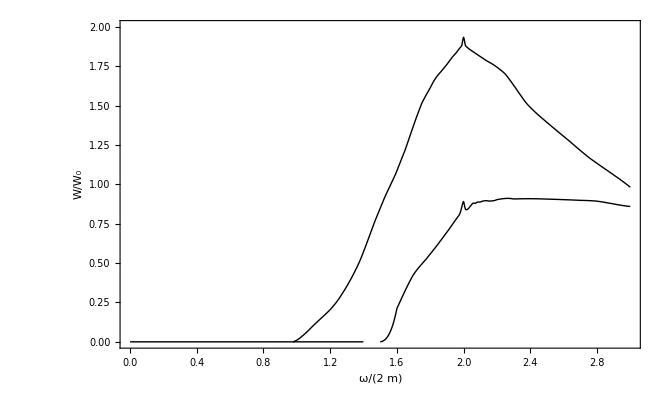

-Graphics-

```mathematica
Show[%,LabelStyle->Directive[FontFamily->"Times",FontSize->24, Black,Thin]]
```

-Graphics-